```mathematica
(* Let's make that diagram Niels was talking about, with the p-e phase space and sample orbits at a few points *)
(* Set parameters *)
e = 0.8;
pOffset=0.2;
p=6+2e+pOffset;
(* Calculate the energy and angular momentum ICs for these parameters *)
E0=√(((p-2-2e)(p-2+2e))/(p(p-3-e^2)));
L0=√((p^2 M0^2)/(p-3-e^2));
(*Initial Conditions*)
r0 = 7.2;
ϕ0 = 0;
t0=0;
θ0=π/2;
M0 = 1;
NullOrTimelike = -1;
```

```mathematica
(* Set the dimension and coordinate system *)
d = 4;
coords={t, r, θ, ϕ};
```

```mathematica
(* Define the metric (Schwarzschild here) *)
f[r_]:=1-(2M)/r;
metric={{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
inverseMetric=Simplify[Inverse[metric]];
```

```mathematica
(* Set initial velocities for t and ϕ above, then find initial r-velocity from normalisation of the vector. Set null or timelike path above *)

u[α_]:=D[coords[[α]][τ],τ];

metricOfτ=metric/.{t->t[τ],r->r[τ],θ->θ[τ],ϕ->ϕ[τ]};

guuEq = Sum[metricOfτ[[a,b]]u[a]u[b], {a, 1, d}, {b, 1, d}];

ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, t'[τ]->-E0/f[r0], θ'[τ]->0, ϕ'[τ]->L0/r0^2, r'[τ]->r'[0]}/.M->M0
```

{r'[0]→0.178511+0. ⅈ}

```mathematica
(* Calculate the Christoffel Symbol *)
Γ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ];

(* Convert the general Christoffel connection to one where the coordinates are functions of time. Really I think this is swapping from the general connection to the connection between different paths or instances of the particle (i.e. we go from r as a coordinate to r_particle(τ) as a component of the position of this object) *)
ΓOfτ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ]/.{t->t[τ], r->r[τ], θ->θ[τ], ϕ->ϕ[τ]};
```

```mathematica
(* Get the geodesic equations for each component *)
timeEq=t''[τ]+Sum[ΓOfτ[[1,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
radialEq=r''[τ]+Sum[ΓOfτ[[2,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
θEq=θ''[τ]+Sum[ΓOfτ[[3,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
ϕEq=ϕ''[τ]+Sum[ΓOfτ[[4,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
```

```mathematica
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==(r'[0]/.ur0), ϕ[0]==ϕ0, ϕ'[0]==L/r0^2, t[0]==0, t'[0]==-En/f[r0], θ[0]==Pi/2, θ'[0]==0};
```

```mathematica
solRange=5000;
eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

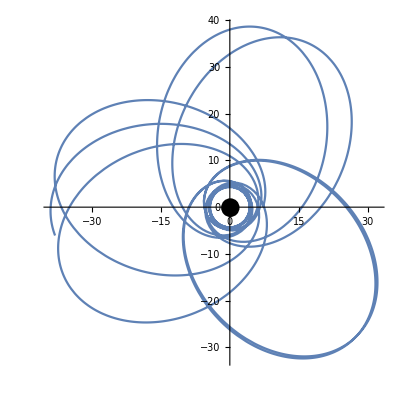

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```

```mathematica
(* Calculate frequencies *) 
tIntegrand=(1/(p-2-2e Cos[χprime]))(1/(1+e Cos[χprime])^2)(1/(√(p-6-2e Cos[χprime])));
tFrequencyFunction[χ_, p_, e_]:=p^2 M√(p-2-2e) √(p-2+2e)NIntegrate[1/(p-2-2e Cos[χprime]) 1/(1+e Cos[χprime])^2 1/(√(p-6-2e Cos[χprime]))/.M->M0,{χprime, 0, χ}];
tFrequencyEq=p0^2 M√(p0-2-2e0) √(p0-2+2e0)Integrate[1/(p0-2-2e0 Cos[χprime]) 1/(1+e0 Cos[χprime])^2 1/(√(p0-6-2e0 Cos[χprime]))/.M->M0,χprime];
(*tFrequencyEqAnalytic=p^2 M√(p-2-2e) √(p-2+2e) Integrate[tIntegrand,χprime]*)
ϕFrequencyEq[χ_, p_, e_]:=√p Integrate[1/(√(p-6-2e Cos[χprime])), {χprime, 0, χ}];
```

```mathematica
(* Definite NIntegrate agreeing with two indefinite Integrates! *)
tFrequencyFunction[2π, p, e]
(tFrequencyEq/.{χprime->π-0.000001, p0->p, e0->e})-(tFrequencyEq/.{χprime->0.0001, p0->p, e0->e})
```

863.492 M

(431.759+0.00186015 ⅈ) M

```mathematica
isolineValue=tFrequencyFunction[2π, 10, 0.5]
Re[2 tFrequencyEq]/.{χprime->π-0.001, e0->0.5, p0->10}
(*ContourPlot[(Re[2 tFrequencyEq]==isolineValue+0.5)/.{χprime->π-0.001, e0->y, p0->x}, {x, 8, 15}, {y, 0.1, 0.9}, PlotPoints->50, MaxRecursion->2]*)
(*eqToSolve=Re[2 tFrequencyEq]/.{χprime->π-0.001 }
solnFore=NSolve[{eqToSolve==isolineValue}, e0]*)
```

433.901 M

2 Re[(216.793+58.9098 ⅈ) M]

{{10,0.5},{9,0.6}}

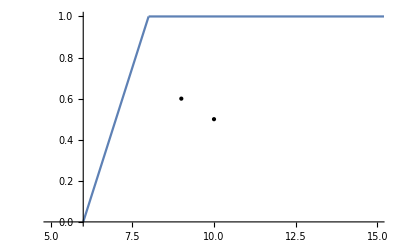

```mathematica
(* Make the graphic *)
points={{10, 0.5}, {9, 0.6}}
Show[Plot[1/2(p-6), {p, 6, 8}], Plot[1, {p, 8, 20}], Graphics[Point[points]], PlotRange->{{5, 15},{0, 1}}]
```

```mathematica
Graphics[Point[points]]
```

-Graphics-

```mathematica
generateOrbit[p0_, e0_]:=Module[{p=Max[p0, 6.2+2e0], e=e0},
E0=√(((p-2-2e)(p-2+2e))/(p(p-3-e^2)));
L0=√((p^2 M0^2)/(p-3-e^2));

r0 = p;
ϕ0 = 0;
t0=0;
θ0=π/2;
M0 = 1;
NullOrTimelike = -1;
ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, t'[τ]->-E0/f[r0], θ'[τ]->0, ϕ'[τ]->L0/r0^2, r'[τ]->r'[0]}/.M->M0;
(*Print[ur0]*)
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==(r'[0]/.ur0), ϕ[0]==ϕ0, ϕ'[0]==L/r0^2, t[0]==0, t'[0]==-En/f[r0], θ[0]==Pi/2, θ'[0]==0};
solRange=5000;
eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]];
(*Print[eomSol]*)
eomSol
(*Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol,{τ,0,5000}],
Graphics[Disk[{0,0}, 2M0]]]]*)
]
```

```mathematica
orbit=generateOrbit[6.2+2(0.8), 0.8];
```

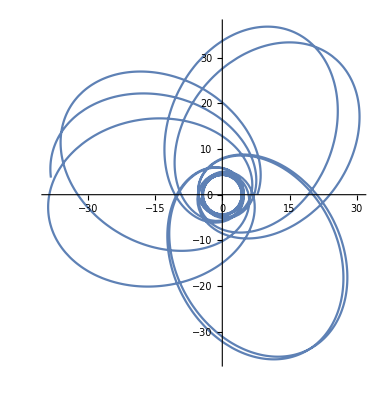

```mathematica
Show[ParametricPlot[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.{orbit},{τ,0,5000}]]
```

{{7,0.1},{8.5,0.9},{10,0.9},{10,0.1},{8.9,0.5}}

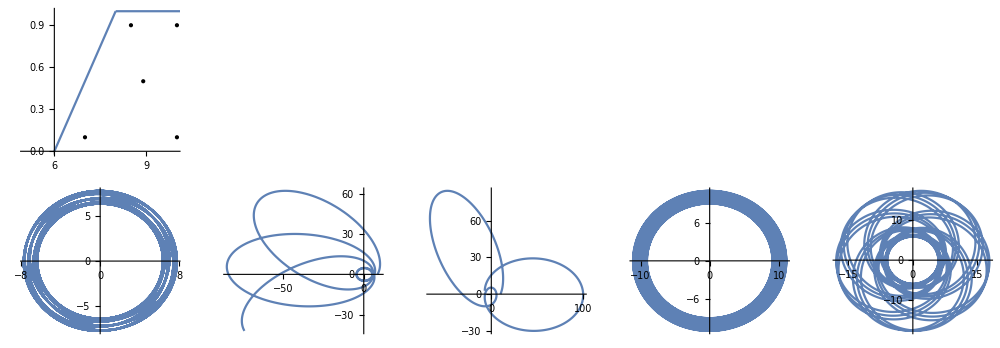

```mathematica
GenerateGraphic[points0_]:=Module[{points=points0},
orbitTable=Table[generateOrbit[points[[i]][[1]], points[[i]][[2]]],{i, Length[points]}];
GraphicsGrid[{{Show[Plot[1/2(p-6), {p, 6, 8}], Plot[1, {p, 8, 20}], Graphics[Point[points]], PlotRange->{{5,10},{0,1}}]},
Table[ParametricPlot[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.{orbitTable[[i]]},{τ,0,5000}], {i, Length[orbitTable]}]}, ImageSize->1000]

]

points={{7, 0.1}, {8.5, 0.9}, {10, 0.9}, {10, 0.1}, {8.9,0.5}}
GenerateGraphic[points]
```

```mathematica
{{7,0.1},{8.5,0.9},{10,0.9},{10,0.1}, {8.9,0.5}}
```

{{7,0.1},{8.5,0.9},{10,0.9},{10,0.1},{8.9,0.5}}

```mathematica
{{7,0.1},{8.5,0.9},{18,0.9}}
```

{{7,0.1},{8.5,0.9},{18,0.9}}

```mathematica
(* Add frequency calculations, fix dimensions of the orbit grid, maybe make look nice, automate point choice *)
```